# Создание данных для обучения нейронной сети

## 1) График функции 2) график функции с контролируемым шумом

Автор: Климов Олег, студент ФН2-51Б

### Код программы

Исходные данные:

```mathematica
(* Задаваемая функция *)
F1[x_]:= Sin[x];
F2[x_]:= Cos[x];
F3[x_]:= Exp[x];
F4[x_]:= x^2;

(* Границы графика *) 
GraphicRange := {{-10, 10},{-10, 10}};

(* Количество изображений *)
kolvo := 10;

(* Размер изображения *)
ImgSize := {1000, 1000};

(* Коэффициенты шума *)
NoiseFactor  := 0.01;
TypeNoise := {"•", 20};


(* Путь сохранения чистого графика *) 
TrainFilepath1 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_train\\sin\\";
TrainFilepath2 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_train\\cos\\";
TrainFilepath3 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_train\\exp\\";
TrainFilepath4 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_train\\pow\\";
(* Путь сохранения шумного графика *) 
TestFilepath1 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_test\\sin\\";
TestFilepath2 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_test\\cos\\";
TestFilepath3 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_test\\exp\\";
TestFilepath4 := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_test\\pow\\";
```

Программа:

```mathematica
(* Количество случайных точек *)
numPoints = NoiseFactor * ImgSize[[1]] * ImgSize[[2]] / 100; 
DataMake[f_, trainpath_, testpath_]:= Module[{TrainFilepath = trainpath, TestFilepath = testpath},
For[i = 1,i < kolvo,i++, 

	(* Задаваемая функция *)
	F2[x_]= i f[x] ;
	
	(* Создание чистого графика *)
	
	(* Чистый график *)
	CleanGraphic = Plot[F2[x], {x, -10, 10}, AspectRatio -> 1, Axes -> True, PlotRange-> GraphicRange,
	Frame->True,FrameTicks-> None, AxesOrigin -> {0,0}, PlotPoints -> 1000, PlotStyle->Black];
	
	(* Путь сохранения чистого графика *) 
	TrainPath = TrainFilepath <> ToString[i]<>".png";
	
	(* Сохранение чистого графика *)
	Export[TrainPath, CleanGraphic, ImageSize -> ImgSize];
	
	(* Создание шумного графика *)
	xCoords = RandomReal[GraphicRange[[1]] , numPoints];       (* Случайные x-координаты     *)
	yCoords = RandomReal[GraphicRange[[2]] , numPoints];       (* Случайные y-координаты     *)
	points = Transpose[{xCoords, yCoords}];                  (* Объединение координат      *)

	(* Шумный график *) 
	NoizeGraphic= Show[CleanGraphic, ListPlot[points, PlotStyle -> Black, PlotMarkers -> TypeNoise]];
	
	(* Путь сохранения шумного графика *) 
	TestPath = TestFilepath <> ToString[i]<>".png";
	
	(* Сохранение шумного графика *)
	Export[TestPath, NoizeGraphic, ImageSize -> ImgSize];
];
];
```

```mathematica
DataMake[F1[x], TrainFilepath1, TestFilepath1];
DataMake[F2[x], TrainFilepath2, TestFilepath2];
DataMake[F3[x], TrainFilepath3, TestFilepath3];
DataMake[F4[x], TrainFilepath4, TestFilepath4];
```

Вывод примера результата:

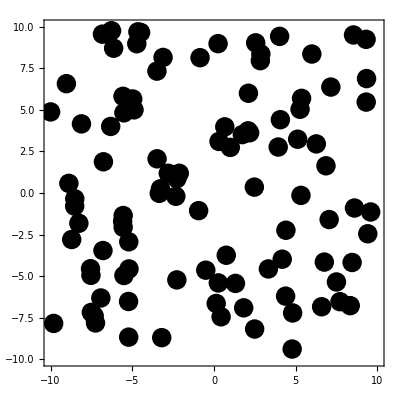

```mathematica
GraphicsRow[{CleanGraphic, NoizeGraphic}, Background -> White]
```